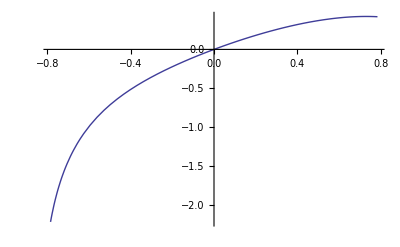

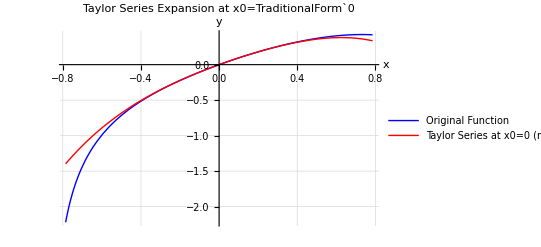
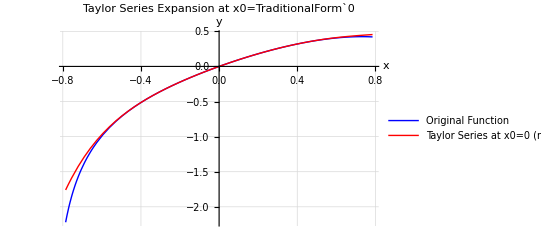
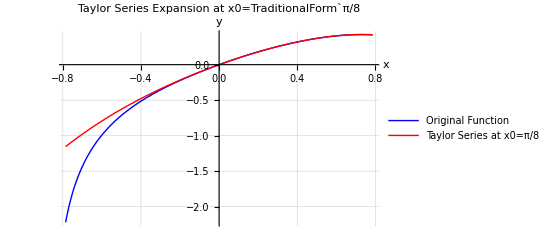
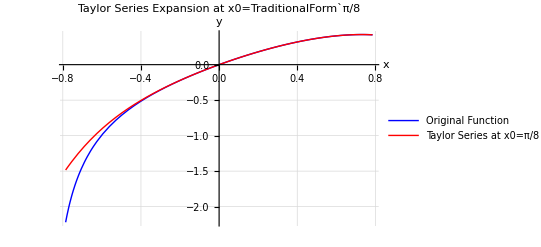
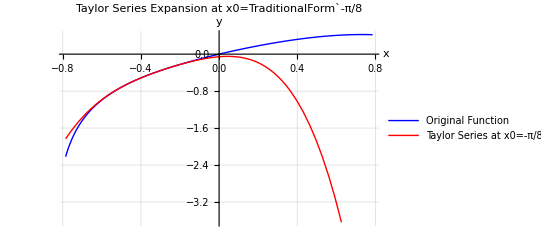
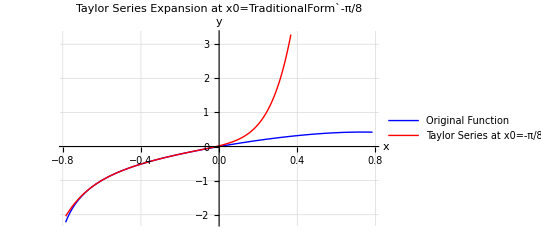
Grid[{-Graphics-
-Graphics-,-Graphics-
-Graphics-,-Graphics-
-Graphics-}]

Taylor coefficients at x0=0:

Order | Coefficient
0 | 0
1 | 1
2 | -1
3 | 1
4 | -14
5 | 65
6 | -376
7 | 2161

```mathematica
f[x_]:=Log[Cos[x^2]+Sin[x]]

xmin=-Pi/4;
xmax=Pi/4;

Plot[f[x],{x,xmin,xmax}]

TaylorSeries[x0_,n_]:=Module[{series},series=Normal[Series[f[x],{x,x0,n}]];Return[series]]

ComparisonPlot[x0_,nterms_]:=Module[{taylor},taylor=TaylorSeries[x0,nterms];
Plot[{f[x],taylor},{x,xmin,xmax},PlotStyle->{Blue,Red},PlotLegends->{"Original Function",StringForm["Taylor Series at x0=`1` (n=`2`)",x0,nterms]},AxesLabel->{"x","y"},PlotLabel->StringForm["Taylor Series Expansion at x0=`1`",x0],GridLines->Automatic]]

x0Values={0,Pi/8,-Pi/8};
Grid[Table[Column[{ComparisonPlot[x0,4],ComparisonPlot[x0,7]}],{x0,x0Values}]]

TaylorCoefficients=Table[D[f[x],{x,n}]/.x->0,{n,0,7}];
Print["Taylor coefficients at x0=0:"];
TableForm[Table[{n,TaylorCoefficients[[n+1]]},{n,0,7}],TableHeadings->{None,{"Order","Coefficient"}}]
```